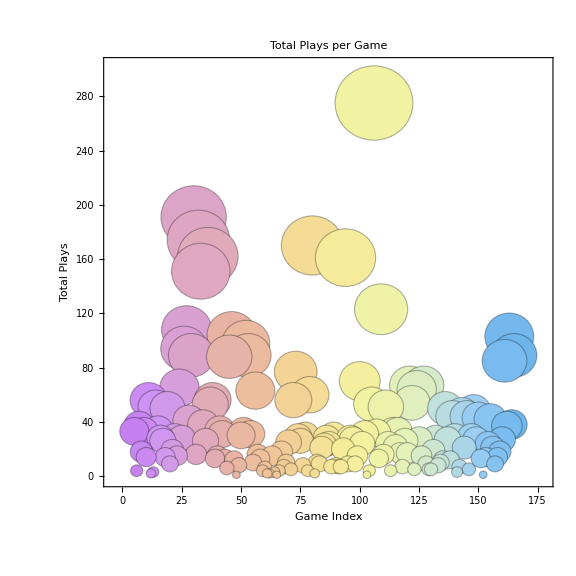

```mathematica
(*Published CSV link*)sheetURL="https://docs.google.com/spreadsheets/d/e/2PACX-1vTf-6AlCge2OKAs4JuAPi5cPtJWmGqjMy27zGyTheWlWiToV4MxwCel0E_YiMiK11QpF69v-EW8bi78/pub?output=csv";

(*Import the data*)
data=Import[sheetURL,"CSV"];

(*Separate headers and values*)
values=Rest[data];

(*Clean and convert total plays to numbers,replace missing/non-numeric with 0*)
cleanValues=values/. {title_,count_}:>{title,If[StringQ[count]&&StringMatchQ[count,NumberString],ToExpression[count],0]};

(*Sort descending by total plays*)
cleanValues=Reverse@SortBy[cleanValues,Last];

(*Build BubbleChart with hover tooltips*)
BubbleChart[Table[Tooltip[{i,cleanValues[[i,2]],cleanValues[[i,2]]},Row[{cleanValues[[i,1]],": ",cleanValues[[i,2]]}]],{i,Length[cleanValues]}],PlotLabel->"Total Plays per Game",AxesLabel->{"Game Index","Total Plays"},ImageSize->Large,ChartStyle->"Pastel"]
```